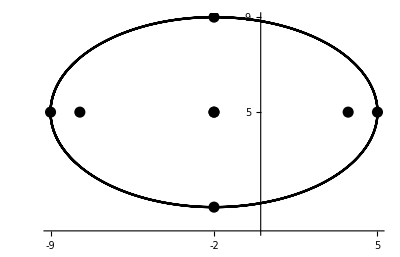

```mathematica
ParametricPlot[
{7Cos[t]-2,4Sin[t]+5},
{t,-10,10},
Ticks->{{-9,-2,5},{-2,5,9}},
PlotStyle->Black,
Epilog->{ 
PointSize[0.02],
Point[{#,5}]&/@{-9,-2,5,-2-Sqrt[33],-2+Sqrt[33]},
Point[{-2,#}]&/@{1,5,9}
}
]
```